2011-05-19

```mathematica
Install["/home/kkumer/gepard/fits/dvem.exe"]
```

LinkObject[/home/kkumer/gepard/fits/dvem.exe/Linux-x86-64/dvem.exe,8,8]

## All DVEM Wilson coefficients

```mathematica
?cdvem
```

cdvem[j, k, rgpdf2, rdaf2, rr2] returns three (unnormalized) DVEM Wilson coefficients C_jk: quark, pure singlet quark and gluon. rgpdf2, rdaf2 and rr2 are ratios of Q2 and squares of GPD factorization, DA factorization and renormalization scales squared, respectively

For low values of λ=Im(j) speed-up is cca. 15x:

```mathematica
AbsoluteTiming[cdvem[0.3+1.7I,2, 2., 2.1, 2.2]]
```

{0.13183,{55.3358+28.4106 ⅈ,0.756184+2.58508 ⅈ,68.9653+71.5926 ⅈ}}

Comparison to DVEM-jk-sum.nb  (which has to be initialized to make next cell evaluatable):

```mathematica
AbsoluteTiming[{CQ[{NLO,verTL},{J,PJ},{K,PK},{CF,CG,β0},{aFgpd,aFda,aR},AccuracyGoal->1],CQsing[{NLO},{J},{K},{CF},{aFgpd},AccuracyGoal->1],Cg[{NLO,short},{J},{K},{CF,CA,β0},{aFgpd,aFda,aR},AccuracyGoal->1]}/.valsH/.vals]
```

{1.4996,{55.2796+28.411 ⅈ,0.758279+2.5961 ⅈ,69.2812+71.4917 ⅈ}}

For larger values of λ=Im(j) speed-up is cca. 30x

```mathematica
AbsoluteTiming[cdvem[0.3+8I,2, 2., 2.1, 2.2]]
```

{0.21155,{99.2751+64.8812 ⅈ,0.242513+0.233666 ⅈ,152.952+132.425 ⅈ}}

Comparison to DVEM-jk-sum.nb  (which has to be initialized to make next cell evaluatable):

```mathematica
AbsoluteTiming[{CQ[{NLO,verTL},{J,PJ},{K,PK},{CF,CG,β0},{aFgpd,aFda,aR},AccuracyGoal->1],CQsing[{NLO},{J},{K},{CF},{aFgpd},AccuracyGoal->1],Cg[{NLO,short},{J},{K},{CF,CA,β0},{aFgpd,aFda,aR},AccuracyGoal->1]}/.{J->0.3+8I}/.valsH/.vals]
```

{5.743882,{99.1219+64.9562 ⅈ,0.244569+0.220335 ⅈ,152.919+132.711 ⅈ}}

## That integral I_(⋁,m)^(μ,n) from Eq. (C.2)

#### Definition of integral (for comparison)

```mathematica
NIntOpt[X_,(opts___)?OptionQ]:=NIntegrate[X,{x,0,1},{z,0,1},{opts}]
```

```mathematica
int[{μ_,m_},{ν_,n_},fz_]:=fz  lnconf[μ,m] conf[ν,n]
```

```mathematica
conf[1/2,k_]=z^(k+1)Hypergeometric2F1[k+2,k+2,2 k+4,z];
conf[3/2,k_]=z^k Hypergeometric2F1[k+1,k+2,2 k+4,z];
conf[5/2,k_]=z^(k-1)Hypergeometric2F1[k,k+2,2 k+4,z];conf[1,1]=1;
```

```mathematica
lnconf[1/2,k_]=(1-x)^(k+1)Hypergeometric2F1[1,1,k+3,1-x z];
lnconf[3/2,k_]=x (1-x)^(k+1)Hypergeometric2F1[1,1,k+2,1-x z];
lnconf[5/2,k_]=x^2 (1-x)^(k+1)Hypergeometric2F1[1,1,k+1,1-x z];lnconf[1,1]=1;
```

#### Checks and timings — speed-up is about 20x

```mathematica
?int2f1
```

int2f1[mu, j, nu, k, ind, acc] does integral f(x) A^mu,j B_nu,k. ind should be 1-5 for f(x)=1, (2-z)z, (1-z)/z, z-2, z, respectively. acc=3-6 is accuracy.

I didn’t find time to implement type checking and conversion so note that arguments mu and nu must be float (not rational), and arguments ind and acc must be integers!

```mathematica
AbsoluteTiming[NIntOpt[Hold[int[{1/2,0.3+I},{3/2,0},1]],AccuracyGoal->4] ]
```

{0.619789,0.725151-0.442752 ⅈ}

```mathematica
AbsoluteTiming[int2f1[0.5, 0.3+I, 1.5, 0, 1,5]]
```

{0.02102,0.725153-0.442754 ⅈ}

```mathematica
AbsoluteTiming[NIntOpt[Hold[int[{3/2,0.3+13I},{1/2,4},(1-z)/z]],AccuracyGoal->4] ]
```

{5.009692,-0.0155968-0.00569115 ⅈ}

```mathematica
AbsoluteTiming[int2f1[1.5, 0.3+13I, 0.5, 4, 3,6]]
```

{0.30014,-0.0155288-0.00572241 ⅈ}

```mathematica
NIntOpt[Hold[int[{1/2,0},{3/2,0.3+I},z-2]],AccuracyGoal->4]
```

-0.946914+0.0786452 ⅈ

```mathematica
int2f1[0.5, 0, 1.5, 0.3+I, 4,5]
```

-0.946997+0.0787707 ⅈ

```mathematica
NIntOpt[Hold[int[{3/2,2},{5/2,0.3+5I},z]],AccuracyGoal->4]
```

-0.002049+0.000443875 ⅈ

```mathematica
int2f1[1.5, 2, 2.5, 0.3+5I, 5,6]
```

-0.00204141+0.00042161 ⅈ

## Some analysis

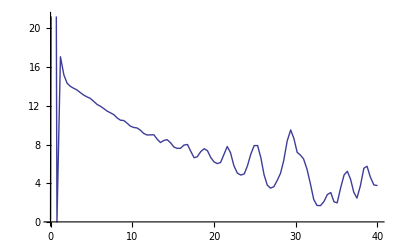

```mathematica
Plot[Im[(cdvem[0.3+λ I,0]⟦3⟧)/(1+λ)],{λ,0,40},PlotPoints->50,MaxRecursion->1]
```

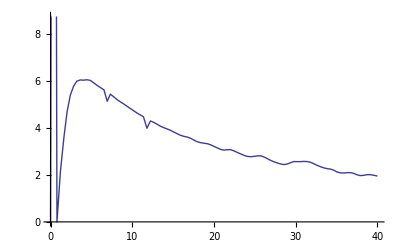

```mathematica
Plot[Im[(cdvem[0.3+λ I,0]⟦1⟧)/(1+λ)],{λ,0,40},PlotPoints->50,MaxRecursion->1]
```